```mathematica
Quit[];
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.11 (2 Sep 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (6 Oct 2019)

by Thomas Hahn

```mathematica
(* Create my topologies. *)
(* 0 loops, 2 incoming legs, 2 outgoing legs.*)
topologies=CreateTopologies[0,2 -> 2];
_Hel=0;
Print[topologies];
```

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

loading generic model file /Users/kpachal/Code/DMSP/FormCalc/FeynArts-3.11/Models/DMsimp_s_spin1_vector.gen

> $GenericMixing is OFF

generic model {DMsimp_s_spin1_vector} initialized

loading classes model file /Users/kpachal/Code/DMSP/FormCalc/FeynArts-3.11/Models/DMsimp_s_spin1_vector.mod

> 46 particles (incl. antiparticles) in 26 classes

> $CounterTerms are ON

> 147 vertices

> 48 counterterms of order 1

classes model {DMsimp_s_spin1_vector} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 1 Classes insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

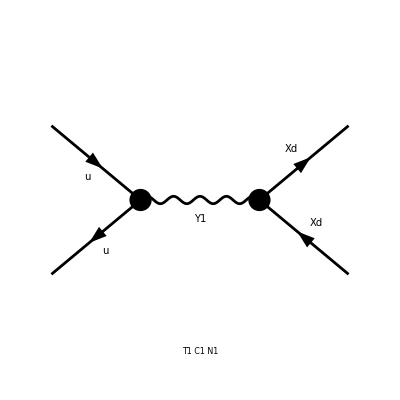

```mathematica
(* ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]} *)
diagvec=InsertFields[topologies,{F[7,{1}],-F[7,{1}]}->{F[13],-F[13]},InsertionLevel->{Classes},
Model->"DMsimp_s_spin1_vector",
GenericModel->"DMsimp_s_spin1_vector"];
Paint[diagvec];
```

```mathematica
ClearProcess[];
amplist = CreateFeynAmp[diagvec];
Print[amplist];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

FeynAmpList[Process→{{F[7,{1}],p1,0,{(2 Q)/3}},{-F[7,{1}],p2,0,{-(2 Q)/3}}}→{{F[13],k1,MXd,{}},{-F[13],k2,MXd,{}}},Model→{DMsimp_s_spin1_vector},GenericModel→{DMsimp_s_spin1_vector},AmplitudeLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Classes==1,Number==1],Integral[],v̄[p2,0].(ⅈ gc75 ga[Lor1].(omSubscript[-])+ⅈ gc75 ga[Lor1].(omSubscript[+])).u[p1,0] ū[k1,MXd].(ⅈ gc76 ga[Lor2].(omSubscript[-])+ⅈ gc76 ga[Lor2].(omSubscript[+])).v[k2,MXd] g[Lor1,Lor2] 1/(-MY1^2+(k1+k2)^2)]]

```mathematica
amp=CalcFeynAmp[amplist,FermionChains->VA];
```

preparing FORM code in /Users/kpachal/fc-amp-9.frm

running FORM...

ok

```mathematica
(* Done with FeynArts! Time to pass the amplitude to FormCalc. *)
(* Squared matrix elements; evaluate *)
squared = SquaredME[amp];
Print[squared];
```

{FF[F1] FFC[F1] Mat[F1,F1],{FF[F1]→-gc75 gc76 Den[S,MY1^2],FFC[F1]→-(gc75Superscript[*]) (gc76Superscript[*]) Den[S,(MY1Superscript[*])^2]}}

```mathematica
(* SquaredME returns a list of {squared, squaredRules}, where we should later apply "squaredRules" to "squared". *)
(* Because of the quarks, we do ColorME too. *)
cleanSquaredME = squared[[1]]//.squared[[2]]//.HelicityME[amp]//FullSimplify
```

> 1 helicity matrix elements

preparing FORM code in /Users/kpachal/fc-hel-10.frm

running FORM...

ok

1/2 gc75 gc76 (T^2+2 MXd^2 (MXd^2+S-T-U)+U^2) (gc75Superscript[*]) (gc76Superscript[*]) Den[S,MY1^2] Den[S,(MY1Superscript[*])^2]

```mathematica
(* We want to sum over polarisations and make them go away: *)
TotalME = PolarizationSum[cleanSquaredME,GaugeTerms->False]//.Subexpr[]//.Abbr[]
```

preparing FORM code in /Users/kpachal/fc-pol-10.frm

running FORM...

ok

1/2 gc75 gc76 (2 MXd^4-4 MXd^2 (MXd^2-S)+T^2+U^2) (gc75Superscript[*]) (gc76Superscript[*]) Den[S,MY1^2] Den[S,(MY1Superscript[*])^2]

```mathematica
(* Convert vertices back to versions we know *)
FinalVertices = TotalME//. M$FACouplings
```

1/2 gVu11 gVXd (2 MXd^4-4 MXd^2 (MXd^2-S)+T^2+U^2) (gVu11Superscript[*]) (gVXdSuperscript[*]) Den[S,MY1^2] Den[S,(MY1Superscript[*])^2]

```mathematica
(* Sort out denominators. *)
WithBWPropagator = FinalVertices//.Den[a_,b_^2]Den[a_, Conjugate[b_]^2]:>1/((a - b^2)^2 + b^2 Gamma^2)
```

(gVu11 gVXd (2 MXd^4-4 MXd^2 (MXd^2-S)+T^2+U^2) (gVu11Superscript[*]) (gVXdSuperscript[*]))/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

```mathematica
(* Tell Mathematica that my couplings and masses are positive real numbers *)
CleanConjugates = Refine[WithBWPropagator, {Element[MY1,Reals],Element[gVXd,Reals],Element[gVu11,Reals], MY1>0}]
```

(gVu11^2 gVXd^2 (2 MXd^4-4 MXd^2 (MXd^2-S)+T^2+U^2))/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

```mathematica
(* Already in Mandelstam variables. *)
(* Now we need quantities we can recognize in the lab. *)
METheta = CleanConjugates//.{U-> 2Mq^2 + 2MXd^2 - S - T,T-> Mq^2 + MXd^2 - (S - Sqrt[S - 4Mq^2]Sqrt[S - 4 MXd^2] CosTheta)/2};
Print[METheta]
```

(gVu11^2 gVXd^2 (2 MXd^4-4 MXd^2 (MXd^2-S)+(Mq^2+MXd^2-S+1/2 (S-CosTheta √(-4 Mq^2+S) √(-4 MXd^2+S)))^2+(Mq^2+MXd^2+1/2 (-S+CosTheta √(-4 Mq^2+S) √(-4 MXd^2+S)))^2))/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

```mathematica
(* TEST: what if I make the incoming and outgoing particles massless? *)
(* Doesn't fix it: not about the massless approximation. *)
METhetaMassless = METheta//.{Mq->0,MXd->0}
MasslessSigma = 2 Pi Integrate[(64 Pi^2)^(-1) METhetaMassless/S,{CosTheta,-1,1}]
MasslessSigmaFinal = Integrate[MasslessSigma,S]
```

(gVu11^2 gVXd^2 (1/4 (-S+CosTheta S)^2+(-S+1/2 (S-CosTheta S))^2))/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

(gVu11^2 gVXd^2 S)/(48 π (Gamma^2 MY1^2+(MY1^2-S)^2))

(gVu11^2 gVXd^2 (-(MY1 ArcTan[(MY1^2-S)/(Gamma MY1)])/Gamma+1/2 Log[Gamma^2 MY1^2+(MY1^2-S)^2]))/(48 π)

```mathematica
(* Test: what if I integrate out t instead of CosTheta? *)
(* If something is wrong with my Mandelstam variable conversion, this could fix it. *)
MEMandelstam = CleanConjugates//.{U-> 2Mq^2 + 2MXd^2 - S - T};
dSigMandelstamdOm = (128 Pi^2)^(-1) MEMandelstam/S
SigmaMandel = 2 Pi Integrate[dSigMandelstamdOm,{T,-S,0}]
```

(gVu11^2 gVXd^2 (2 MXd^4-4 MXd^2 (MXd^2-S)+(2 Mq^2+2 MXd^2-S-T)^2+T^2))/(256 π^2 S (Gamma^2 MY1^2+(-MY1^2+S)^2))

(gVu11^2 gVXd^2 (6 Mq^4+3 MXd^4+3 Mq^2 (4 MXd^2-S)+3 MXd^2 S+S^2))/(192 π (Gamma^2 MY1^2+(MY1^2-S)^2))

```mathematica
(* Continue test: integrate out S here. *)
(* Different answer, still wrong...? *)
(* Is it actually the same? *)
SigmaMandelFinal = Integrate[SigmaMandel,S]
```

(gVu11^2 gVXd^2 (S-((6 Mq^4+12 Mq^2 MXd^2+3 MXd^4-Gamma^2 MY1^2-3 Mq^2 MY1^2+3 MXd^2 MY1^2+MY1^4) ArcTan[(MY1^2-S)/(Gamma MY1)])/(Gamma MY1)-1/2 (3 Mq^2-3 MXd^2-2 MY1^2) Log[Gamma^2 MY1^2+(MY1^2-S)^2]))/(192 π)

```mathematica
(* This is our matrix element. *)
(* For this to be well behaved, |M|^2 should approach a constant as s-> 0 or s-> infinity. *)
(* We show that it does (bar the fact that it is ill-defiend below S = MXd^2). *)
TestZero = METheta//.S->0
TestInf = Limit[METheta,S->Infinity]
```

(gVu11^2 gVXd^2 (-2 MXd^4+(Mq^2+MXd^2-2 CosTheta √(-Mq^2) √(-MXd^2))^2+(Mq^2+MXd^2+2 CosTheta √(-Mq^2) √(-MXd^2))^2))/(2 (Gamma^2 MY1^2+MY1^4))

1/4 (1+CosTheta^2) gVu11^2 gVXd^2

```mathematica
(* Now to compute the cross section. *)
(* CONFIDENT TO HERE *)
(* Golden rule: dSigma/dOmega =(appx) 1/(64 Pi^2 S) |M^2| *)
(* Does the above apply to massless particles only? *)
dSigdOm = (64 Pi^2)^(-1) METheta/S
```

1/(128 π^2 S (Gamma^2 MY1^2+(-MY1^2+S)^2))gVu11^2 gVXd^2 (2 MXd^4-4 MXd^2 (MXd^2-S)+(Mq^2+MXd^2-S+1/2 (S-CosTheta √(-4 Mq^2+S) √(-4 MXd^2+S)))^2+(Mq^2+MXd^2+1/2 (-S+CosTheta √(-4 Mq^2+S) √(-4 MXd^2+S)))^2)

```mathematica
(* Total differential cross section: integral over 2 Pi d(CosTheta) from -1 to 1 *)
Sigma = 2 Pi Integrate[dSigdOm,{CosTheta,-1,1}]
```

(gVu11^2 gVXd^2 (3 Mq^4+2 Mq^2 (5 MXd^2-2 S)+S (2 MXd^2+S)))/(48 π (Gamma^2 MY1^2+(MY1^2-S)^2) S)

```mathematica
(* Does this still behave as expected? *)
TestSigmaZero = Limit[Sigma,S->2 MXd]
TestSigmaInf = Limit[Sigma,S->Infinity]
```

(gVu11^2 gVXd^2 (3 Mq^4+2 MXd (2 MXd+2 MXd^2)+2 Mq^2 (-4 MXd+5 MXd^2)))/(96 MXd (Gamma^2 MY1^2+(-2 MXd+MY1^2)^2) π)

0

(20000+S)/(48 π (25.+(250000-S)^2))

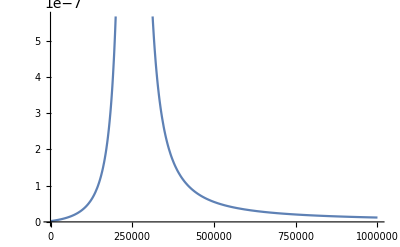

```mathematica
(* Plot the cross section. It should drop off roughly as 1/s. *)
Plottable = Sigma//.{MXd-> 100, MY1->500, gVu11->1, gVXd->1, Mq->0, Gamma->0.01}
Plot[Plottable,{S, 100, 1000000}]
```

```mathematica
(* Indeed, above S which gives resonance, it does. *)
```

```mathematica
(* Last part of phase space integral... *)
(* Is this even the right thing to do? *)
SigmaFinal = Integrate[Sigma,S]
```

1/(96 Gamma MY1^2 (Gamma^2+MY1^2) π)gVu11^2 gVXd^2 (-2 MY1 (3 Mq^4+2 MXd^2 MY1^2+MY1^4+2 Mq^2 (5 MXd^2-2 MY1^2)+Gamma^2 (-4 Mq^2+2 MXd^2+MY1^2)) ArcTan[(MY1^2-S)/(Gamma MY1)]+Gamma ((-3 Mq^4-10 Mq^2 MXd^2+Gamma^2 MY1^2+MY1^4) Log[Gamma^2 MY1^2+(MY1^2-S)^2]+2 Mq^2 (3 Mq^2+10 MXd^2) Log[-S]))

```mathematica
(* Last term is the problem. The log functions are not OK. They grow very gradually towards infinity *)
(* such that ultimately this is divergent. Feel as though they should not be here. *)
```

```mathematica
(* Compare this expression to the one where I integrated out T... *)
FullSimplify[SigmaFinal]==FullSimplify[SigmaMandelFinal]
```

1/(96 Gamma MY1^2 (Gamma^2+MY1^2) π)gVu11^2 gVXd^2 (-2 MY1 (3 Mq^4+2 MXd^2 MY1^2+MY1^4+2 Mq^2 (5 MXd^2-2 MY1^2)+Gamma^2 (-4 Mq^2+2 MXd^2+MY1^2)) ArcCot[(Gamma MY1)/(MY1^2-S)]+Gamma (-3 Mq^4-10 Mq^2 MXd^2+Gamma^2 MY1^2+MY1^4) Log[Gamma^2 MY1^2+(MY1^2-S)^2]+2 Gamma Mq^2 (3 Mq^2+10 MXd^2) Log[-S])==1/(384 Gamma MY1 π)gVu11^2 gVXd^2 (-2 (3 (2 Mq^4+4 Mq^2 MXd^2+MXd^4)-(Gamma^2+3 (Mq-MXd) (Mq+MXd)) MY1^2+MY1^4) ArcCot[(Gamma MY1)/(MY1^2-S)]+Gamma MY1 (2 S+(-3 Mq^2+3 MXd^2+2 MY1^2) Log[Gamma^2 MY1^2+(MY1^2-S)^2]))